\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

# Elementos de Programação

Funções

Listas

Programação Imperativa

Programação Funcional

Programação baseada em Padrões

Recursão

Interação com o Sistema Operacional

Depuração e Análise dde Desempenho

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Filosofia Basica

• Tudo são expressões
	• Funções transformam expressões em expressões
	• Integracao com Sistema Operacional, Java, C

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Bibliografia

• Maeder, R. E. "The Mathematica Programer"
• Maeder, R. E. "The Mathematica Programer II"
• Wagner, D. B., "Power Programming with Mathematica: The kernel"
• Maeder, R. E. "Computer Science with Mathematica"
• Vardi, I. "Computational Recreations with Mathematica"

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Expressoes

head[part1, part2, ...]
	Todas as expressões no Mathematica podem ser escritas utilizando apenas colchetes, átomos e vírgulas.
	Átomos:
	             - Símbolos
	             - Números
	             - Strings

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Expressões

```mathematica
A={1,2/3,π,1.72,a+b,{Banana},α}
Head[A]
FullForm[A]
```

{1,2/3,π,1.72,a+b,{Banana},α}

List

List[1,Rational[2,3],Pi,1.72,Plus[a,b],List[Banana],\[Alpha]]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Funções

Existem duas formas de atribuir um valor a um símbolo no Mathematica: =(Set) e := (SetDelayed).

```mathematica
xset=b+c;
xdel:=b+c;
c=3
xset
xdel
```

3+b

3

```mathematica
c=4
Print["xset= ",xset]
Print["xdel= ",xdel]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Aplicando Funções

Forma Covarde

```mathematica
f[x]
```

f[x]

Mais Corajosa

```mathematica
f @ x
```

f[x]

Forma pos fixada

```mathematica
x // f
```

f[x]

Um pouco mais interessante

```mathematica
x~f~y
```

f[x,y]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Definindo Funções

A maneira mais simples de definir uma função e:

```mathematica
f[x_]:=x+x;
```

```mathematica
f[2]
```

4

```mathematica
f[a]
```

2 a

```mathematica
f[{1,2,3}]
```

{2,4,6}

```mathematica
f["bobo"]
```

2 bobo

```mathematica
f["bobo"]//FullForm
```

Times[2,"bobo"]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## O enigmatico significado do "_"

As funções no Mathematica não são equivalentes as definições de função na Matematica! No Mathematica uma função é uma operação de reconhecimento de padrões!
	O "_" nos permite restringir o escopo de uma função!

```mathematica
freal[x_Real]:=Exp[x] ;(* So para Reais *)
fint[x_Integer]:=Exp[x]; (* Para Inteiros *)
```

```mathematica
fint[2]
freal[2.]
fint[2.]
freal[2]
```

ⅇ^2

7.38906

fint[2.]

freal[2]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Usos mais esotericos do "_"

```mathematica
feso[x_?(#>0&)]:=Cos[x]
```

```mathematica
feso[2]
feso[-2]
```

Cos[2]

feso[-2]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Funcoes Puras

Um usuário experiente do Mathematica não deve recorrer a forma anterior e covarde  de definir funções. Pois esta forma aumenta a legibilidade do Codigo! Uma forma muito mais ilegível e a seguinte:

```mathematica
(#^2+1)&[{1,2,3}]
```

{2,5,10}

```mathematica
g:=(#^2+1)&
```

```mathematica
x//g
```

1+x^2

```mathematica
h:=(#1^2+#2^3+2)&;
```

```mathematica
h[a,b]
```

2+a^2+b^3

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Aumentando a diversão

```mathematica
Trans[func_,a_]:=func[a+x]
```

```mathematica
Trans[#^2&,a]
```

(a+x)^2

Para desertores covardes também é possível usar a forma mais legível, mas menos poética:

```mathematica
Clear[f];
f=Function[x,x^2];
Trans[f,a]
```

Function[x,x^2]

(a+x)^2

## Exercício

Construa uma função que implemente rotações em duas dimensões e aplique isso para gerar gráficos rotacionados  da função f(x,y)=x^2-y^2.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Aplicando Restrições

```mathematica
g[x_]:=1 /; x<1
g[x_]:=2/; x>=1 && x<2
g[x_]:=3/; x≥2
```

```mathematica
Plot[g[x],{x,0,3},PlotStyle->{Thickness[0.02]}]
```

## Exercícios

Implemente uma função que calcula o IR de um assalariado brasileiro com uma única fonte de renda.

## Programação Imperativa

A programação imperativa é aquela utilizada em linguagens como C e Fortran. Além dos comandos de atribuição estas linguagens incluem comandos para lidar com processamento repetitivo. Para ilustrar estas técnicas vou atacar um problema trivial: determinar se um número é primo.

```mathematica
(* Vergonhasemente Burro *)
num=2007;
Do[If[Floor[num/i]==num/i, Print[{i,"Não Primo"}]],{i,2,num-1}]
```

```mathematica
(* Melhor usando For *)
num=13;
For[i=2,Floor[num/i]!=num/i,i++,];
If[i==num,Print["Primo"],Print["Não Primo"]]
```

Primo

```mathematica
(* Usando While *)
num=13;
i=2;
While[(i<num-1) && (Floor[num/i]!=N[num/i]),
i++;      
]
If[i==num-1,Print["Primo"],Print["Não Primo"]]
```

Primo

```mathematica
(* Melhor, Usando um velho e conhecido teorema da Teoria dos Números *)
num=13;
i=2;
While[(i<Sqrt[num]) && (Floor[num/i]!=N[num/i]),
i++;      
]
If[i==Ceiling[Sqrt[num]],Print["Primo"],Print["Não Primo"]]
```

Primo

◀     |     ▶

## Exercício

Determine todos os elementos químicos que são mais abundantes no corpo humano que no Universo. Descubra qual é o elemento de menor número atômico que satisfaz essa propriedade. 

Descubra qual é o elemento com maior número atômico que não possui isótopos.

## Programação Funcional

A programacao Funcional no Mathematica é muito poderosa, mas também perigosa. Além de tornar os progrmas mais difíceis de modificar eventualmente pode causar perdas de desempenho  se mal utilizada. Mas é difícil resistir, com poucas linhas pode se realizar programas que custariam muitas linhas em outras formas de programação.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Map (Por Cada)

```mathematica
Clear[f];
Map[f,{1,2,3}] (* ou *)
f/@ {1,2,3}
```

{f[1],f[2],f[3]}

{f[1],f[2],f[3]}

```mathematica
(#^2+Cos[#])&/@L1
```

{6241+Cos[79],7921+Cos[89],121+Cos[11],16129+Cos[127],241081+Cos[491]}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Apply (Oba Oba)

```mathematica
Apply[f,{1,2,3}]
f@@{1,2,3}
```

f[1,2,3]

f[1,2,3]

Lamentavelmente, apesar da aura mágica que exala do comando Apply ele é só um comandinho chinelo. Vejamos:

```mathematica
FullForm[{1,2,3}]
FullForm[f@@{1,2,3}]
```

List[1,2,3]

f[1,2,3]

Meio bobo. Mas ...

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## "Por cada" e "Oba-oba" juntos fazem a festa

```mathematica
Plus @@ (#^2& /@  {a,b,c,d})
```

a^2+b^2+c^2+d^2

```mathematica
Momentum[n_Integer,L_List]:=Plus@@(#^2&/@ L)/Length[L]//N;
Momentum[4,Table[i,{i,1,100}]]
```

3383.5

```mathematica
(Plus @@ (Sin[#]& /@ Table[x,{x,0, Pi,0.01}]))*0.01
```

1.99999

## Exercício

Determine a média e o desvio padrão da razão entre número atômico e massa dos elementos químicos. Represente graficamente esses valores com relação ao número atômico.Selecione os elementos que possuem um valor alto e elementos com valores baixos. (Ou seja aqueles que desviam mais de um desvio padrão do valor da média. 

Calcule a taxa de variação média dos valores das ações do IBOVESPA. Selecione usando a mesma estratégia as com variação excepcional.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Variantes do Map e Apply

Para começo de conversa o Map aceita um parametro a mais.

```mathematica
LLouca={1,{1,2},{1,{1,2}},{1,{1,1{1,1}}}};
Map[f,LLouca]
Map[f,LLouca,2]
Map[f,LLouca,3]
Map[f,LLouca,{2}]
```

{f[1],f[{1,2}],f[{1,{1,2}}],f[{1,{1,{1,1}}}]}

{f[1],f[{f[1],f[2]}],f[{f[1],f[{1,2}]}],f[{f[1],f[{1,{1,1}}]}]}

{f[1],f[{f[1],f[2]}],f[{f[1],f[{f[1],f[2]}]}],f[{f[1],f[{f[1],f[{1,1}]}]}]}

{1,{f[1],f[2]},{f[1],f[{1,2}]},{f[1],f[{1,{1,1}}]}}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Variantes do Map e do Apply

```mathematica
MapAt[f,LLouca,2]
```

{1,f[{1,2}],{1,{1,2}},{1,{1,{1,1}}}}

```mathematica
MapIndexed[f,{a,b,c}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapThread[f,{{a,A,α},{b,B,β},{c,C,χ}}]
```

{f[a,b,c],f[A,B,C],f[α,β,χ]}

## Exercício

Considere uma variável que pode assumir n valores diferentes. Implemente uma função que determine a frequência com que cada elemento aparece na ‘serie e avalie a entropia S=-∑ p_i log p_(i .)Defina 0 log 0=0. A função deve ser genérica.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Se livrando das malditas chaves

As chaves no Mathematica são extremamente importantes, mas eventualmente aparecem nos lugares mais inadequados. Daí temos que eliminá-las, usando alguns truques.

```mathematica
LLouca
Flatten[LLouca] (* Morte as Chaves !! *)
Flatten[LLouca,1]
Flatten[LLouca,2]
FlattenAt[LLouca,2]
```

{1,{1,2},{1,{1,2}},{1,{1,{1,1}}}}

{1,1,2,1,1,2,1,1,1,1}

{1,1,2,1,{1,2},1,{1,{1,1}}}

{1,1,2,1,1,2,1,1,{1,1}}

{1,1,2,{1,{1,2}},{1,{1,{1,1}}}}

```mathematica
L={{1,2,3,{2,3}}}
L[[1]] (* Truque de 1 Milhao de Dolares *)
```

{{1,2,3,{2,3}}}

{1,2,3,{2,3}}

Agora um truque mais dificil.

```mathematica
fLouca[a_,b_,c_]=a*b+c;
LL={1,2,3};
fLouca[LL]
fLouca[Sequence[LL]]
fLouca[Sequence @@ LL] (* Uauuu !!!*)
```

fLouca[{1,2,3}]

fLouca[{1,2,3}]

5

## Coisas mais bizarras

```mathematica
Outer[List,{1,2,3,4},{a,b,c}]
```

```mathematica
{{{1,a},{1,b},{1,c}},{{2,a},{2,b},{2,c}},{{3,a},{3,b},{3,c}},{{4,a},{4,b},{4,c}}}
```

```mathematica
Inner[Plus, {a,b,c},{e,f,g},Times]
```

(a+e) (b+f) (c+g)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Substituicao de Padroes

"... the underlying mechanism for implementing all other programming constructs" 
									R. Maeder

	 O assunto é vasto e complexo, assim só nos resta  concentrar na ponta do Iceberg. Infelizmente igualmente vasto e igualmente complexo.  
	 A estrutura básica de um Padrao e:	
	Pattern_Head
	Padrões podem ser substituidos por outros padroes
	/. Padrao -> Substituicao

```mathematica
{a,b,c}/.a->1
```

{1,b,c}

```mathematica
{a,b,{a,c}}/.a->1
```

{1,b,{1,c}}

```mathematica
{a,b,{a,c}}/.{a->1,b->2}
```

{1,2,{1,c}}

```mathematica
{a,b,{a,b},{a,b,c}}/.{x_,y_}->x
```

{a,b,a,{a,b,c}}

```mathematica
{a,b,{a,b},{a,b,c}}/.{x_,_}->x
```

{a,b,a,{a,b,c}}

```mathematica
{{a,b},{c,d},{a,b,c}}/.{___,x_,___}->x
```

{a,b}

```mathematica
f[x]+g[x]/.x_f->a
```

a+g[x]

```mathematica
expr=Sqrt[u-1]/Sqrt[u^ 2-1];
```

```mathematica
expr/. 1/Sqrt[y_]->1/Sqrt[Factor[y]]
```

(√(-1+u))/(√(-1+u^2))

```mathematica
expr/.1/Sqrt[y_]:>1/Sqrt[Factor[y]]
```

(√(-1+u))/(√((-1+u) (1+u)))

## // Substituição Recursiva

Para realizar uma substituição de forma recursiva usamos //. Neste caso a regra é aplicada até a exaustão

## A verdade sobre as funções

Na verdade as funções são regras de transformação que são válidas para todas as expressoes do Mathematica.

```mathematica
h[5]//.{h[0]:>1,h[n_] :> n*h[n-1]}
```

5 h[4]

```mathematica
h[5]//.{h[0]->1,h[n_]->n*h[n-1]}
```

120

## :> Substituição Postergada

De forma equivalente a atribuição postergada podemos fazer uma substituição postergada.

```mathematica
{x,x,x}/.x-> Random[]
```

{0.713691,0.713691,0.713691}

```mathematica
{x,x,x}/.x:> Random[]
```

{0.287122,0.725548,0.0662011}

## Ordenamento de Vetores

```mathematica
lis={8,-4,5,6,7,9,9};
lis//.{z___,x_,y_,w___}/;x>y:>{z,y,x,w}
```

{-4,5,6,7,8,9,9}

◀     |     ▶

## Recursão

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
Fold[f,t,{x,y,z}]
```

f[f[f[t,x],y],z]

```mathematica
Fold[Plus,t,{x,y,z}] (* Nem tao inutil assim *)
```

t+x+y+z

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Interação com o sistema Operacional

```mathematica
Expand[(x+y)^3]>>tmp
!!tmp
```

```mathematica
Export["out.dat",{{5.7,4.3},{-1.2,7.8}}]
Import["out.dat","Table"]
```

```mathematica
In[1]:=Directory[]
SetDirectory["Examples"]
FileNames["Test*.m"]
```

```mathematica
!date
RunThrough["cat",789]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Depuração e Desempenho

- Use funcoes do sistema
	- Use programacao funcional
	- Use aritmetica real
	- Avalie sempre que possivel
	- Evite Append and Prepend
	- Não modifique listas localmente
	- Cuidado com padrões Ineficientes
	- Use funções puras
	
	Ferramentas 
	- Timing
	- Trace

## Uso do Trace

```mathematica
lis={8,-4,5,6,7,9,9};
Trace[lis//.{z___,x_,y_,w___}/;x>y:>{z,y,x,w}]
```

{{lis,{8,-4,5,6,7,9,9}},{{z___,x_,y_,w___}/;x>y:>{z,y,x,w},{z___,x_,y_,w___}/;x>y:>{z,y,x,w}},{8,-4,5,6,7,9,9}//.{z___,x_,y_,w___}/;x>y:>{z,y,x,w},{8>-4,True},{-4>8,False},{8>5,True},{-4>5,False},{5>8,False},{8>6,True},{-4>5,False},{5>6,False},{6>8,False},{8>7,True},{-4>5,False},{5>6,False},{6>7,False},{7>8,False},{8>9,False},{9>9,False},{-4,5,6,7,8,9,9}}

◀     |     ▶

## Uso do Timing

```mathematica
lis=Table[Random[Real,{0,1}],{200}];
```

```mathematica
Timing[lis//.{z___,x_,y_,w___}/;x>y:>{z,y,x,w}]
```

{2.25513,{0.0068426,0.00703507,0.00940596,0.0123914,0.0127107,0.0129854,0.0187128,0.0268013,0.0286738,0.0339085,0.0434249,0.0438184,0.0451433,0.0463047,0.0493754,0.0596213,0.064725,0.0684072,0.076826,0.07915,0.0869645,0.0902879,0.0926872,0.0941031,0.0985918,0.0992469,0.103647,0.106289,0.109668,0.113974,0.118557,0.118962,0.120326,0.12081,0.125312,0.133037,0.133304,0.134736,0.136203,0.137555,0.148052,0.155664,0.156622,0.164699,0.173064,0.184441,0.19473,0.205751,0.208845,0.218737,0.229619,0.231135,0.231447,0.236461,0.24201,0.246093,0.252935,0.258802,0.276711,0.285435,0.291358,0.302051,0.302445,0.306709,0.318099,0.318934,0.322764,0.323531,0.324168,0.325266,0.327581,0.327807,0.33351,0.335395,0.340627,0.341158,0.341954,0.345118,0.352205,0.358965,0.359798,0.36006,0.36309,0.364484,0.384682,0.38729,0.387489,0.391826,0.394145,0.397254,0.401914,0.40728,0.414266,0.416025,0.42369,0.428082,0.430986,0.434934,0.439088,0.44,0.447057,0.454934,0.465401,0.471167,0.473756,0.477369,0.478752,0.484543,0.489206,0.506679,0.509775,0.516904,0.529979,0.535534,0.539468,0.55082,0.560691,0.564297,0.567737,0.580182,0.581081,0.588238,0.600582,0.60307,0.607408,0.613649,0.614443,0.619086,0.621065,0.637215,0.64708,0.653913,0.670223,0.674666,0.685643,0.688224,0.700425,0.700613,0.713515,0.71353,0.717445,0.726815,0.741183,0.741404,0.743139,0.747324,0.75038,0.75239,0.759384,0.76087,0.763776,0.770252,0.775691,0.775706,0.778783,0.779658,0.780464,0.780693,0.787044,0.789403,0.792138,0.798973,0.811179,0.813806,0.834325,0.837043,0.838221,0.841168,0.844846,0.852691,0.854265,0.857237,0.85729,0.881308,0.886033,0.895343,0.896086,0.903554,0.903639,0.905451,0.908355,0.914056,0.914394,0.921091,0.931121,0.94174,0.948863,0.968541,0.971264,0.972346,0.974241,0.978335,0.981719,0.982463,0.988071,0.988322,0.99344,0.995283,0.999725,0.999985}}

```mathematica
Timing[Sort[lis]]
```

{0.000073,{0.0068426,0.00703507,0.00940596,0.0123914,0.0127107,0.0129854,0.0187128,0.0268013,0.0286738,0.0339085,0.0434249,0.0438184,0.0451433,0.0463047,0.0493754,0.0596213,0.064725,0.0684072,0.076826,0.07915,0.0869645,0.0902879,0.0926872,0.0941031,0.0985918,0.0992469,0.103647,0.106289,0.109668,0.113974,0.118557,0.118962,0.120326,0.12081,0.125312,0.133037,0.133304,0.134736,0.136203,0.137555,0.148052,0.155664,0.156622,0.164699,0.173064,0.184441,0.19473,0.205751,0.208845,0.218737,0.229619,0.231135,0.231447,0.236461,0.24201,0.246093,0.252935,0.258802,0.276711,0.285435,0.291358,0.302051,0.302445,0.306709,0.318099,0.318934,0.322764,0.323531,0.324168,0.325266,0.327581,0.327807,0.33351,0.335395,0.340627,0.341158,0.341954,0.345118,0.352205,0.358965,0.359798,0.36006,0.36309,0.364484,0.384682,0.38729,0.387489,0.391826,0.394145,0.397254,0.401914,0.40728,0.414266,0.416025,0.42369,0.428082,0.430986,0.434934,0.439088,0.44,0.447057,0.454934,0.465401,0.471167,0.473756,0.477369,0.478752,0.484543,0.489206,0.506679,0.509775,0.516904,0.529979,0.535534,0.539468,0.55082,0.560691,0.564297,0.567737,0.580182,0.581081,0.588238,0.600582,0.60307,0.607408,0.613649,0.614443,0.619086,0.621065,0.637215,0.64708,0.653913,0.670223,0.674666,0.685643,0.688224,0.700425,0.700613,0.713515,0.71353,0.717445,0.726815,0.741183,0.741404,0.743139,0.747324,0.75038,0.75239,0.759384,0.76087,0.763776,0.770252,0.775691,0.775706,0.778783,0.779658,0.780464,0.780693,0.787044,0.789403,0.792138,0.798973,0.811179,0.813806,0.834325,0.837043,0.838221,0.841168,0.844846,0.852691,0.854265,0.857237,0.85729,0.881308,0.886033,0.895343,0.896086,0.903554,0.903639,0.905451,0.908355,0.914056,0.914394,0.921091,0.931121,0.94174,0.948863,0.968541,0.971264,0.972346,0.974241,0.978335,0.981719,0.982463,0.988071,0.988322,0.99344,0.995283,0.999725,0.999985}}

◀     |     ▶

## Exercício

Compare o desempenho do algoritmo proposto para ordenar vetores usando o método proposto acima com o método do Mathematica ordenando vetores de tamanhos 10, 50, 100, 500 e 1000 e medindo os tempos. Plote os resultados em escalalog-log.

## Lições

Programas curtos nem sempre são eficientes

Programas elegantes nem sempre são eficientes

Muitas vezes em computação vale mais a pena copiar do que reinventar

◀     |     ▶

## Um exemplo Legal

◀     |     ▶

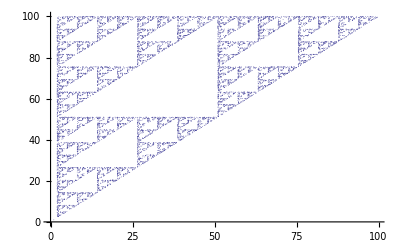

```mathematica
A={{{0.5,0},{0,0.5}},{{0.5,0},{0,0.5}},{{0.5,0},{0,0.5}}};
b={{1,1},{1,50},{50,50}};
IFS[A_,b_][x_]:=Module[{n},
n=Random[Integer,{1,Length[A]}];
A[[n]].x+b[[n]]
]
lis=NestList[IFS[A,b],{1,1},10000];
ListPlot[lis,PlotStyle->{PointSize[0.001]}]
```

## Exercício

Os primos de Mersemme possuema forma: 2^p-1, onde p é primo.

Desenvolva um programa que expresse um número em uma base binária. Não vale usar uma função  do Mathematica.

Escreva exemplos de números  primos de Merseme na base 2

Determine o menor valor de p tal que o primo de Merseme correspondente não seja primo.

◀     |     ▶

## Exercício

Com base no código acima desenhe o triângulo de Sierspinski girado de 180^o.

Gera uma variante do triangulo de Sierspinsky, chamado Quadrado de .... (Coloque seu nome na elipse)

◀     |     ▶